```mathematica
ex={{"Per-Node\nLog Parsing",8.3/6},{"Preprocessing",3.5},{"Clustering",.2}}
BarChart[Last[#]&/@ex,ChartLabels->Placed[(First[#]&/@ex),Top],Frame->True,ChartElementFunction->"GlassRectangle",Axes->True,ChartStyle->"Pastel",FrameLabel->{"Compute Type","CPU usage per node (s)"},BaseStyle->{FontSize->40,FontFamily->"Calibri"}]
```

{{Per-Node
Log Parsing,1.38333},{Preprocessing,3.5},{Clustering,0.2}}

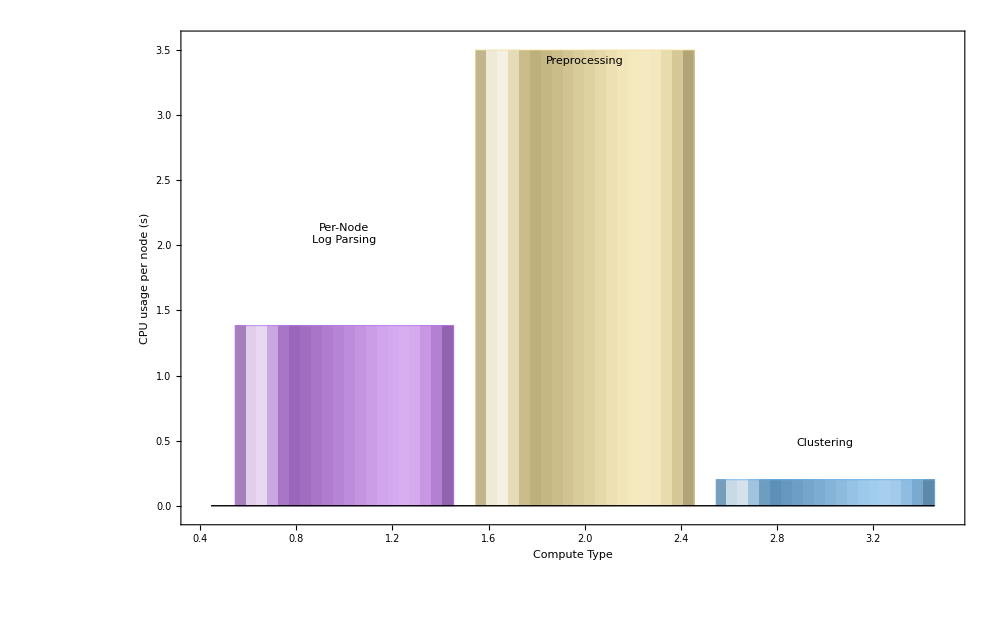

{{Failed node,2},{Node 5%
slower,2},{Node 1%
slower,3},{50% of log
is junk,2},{99% of log
is junk,4}}

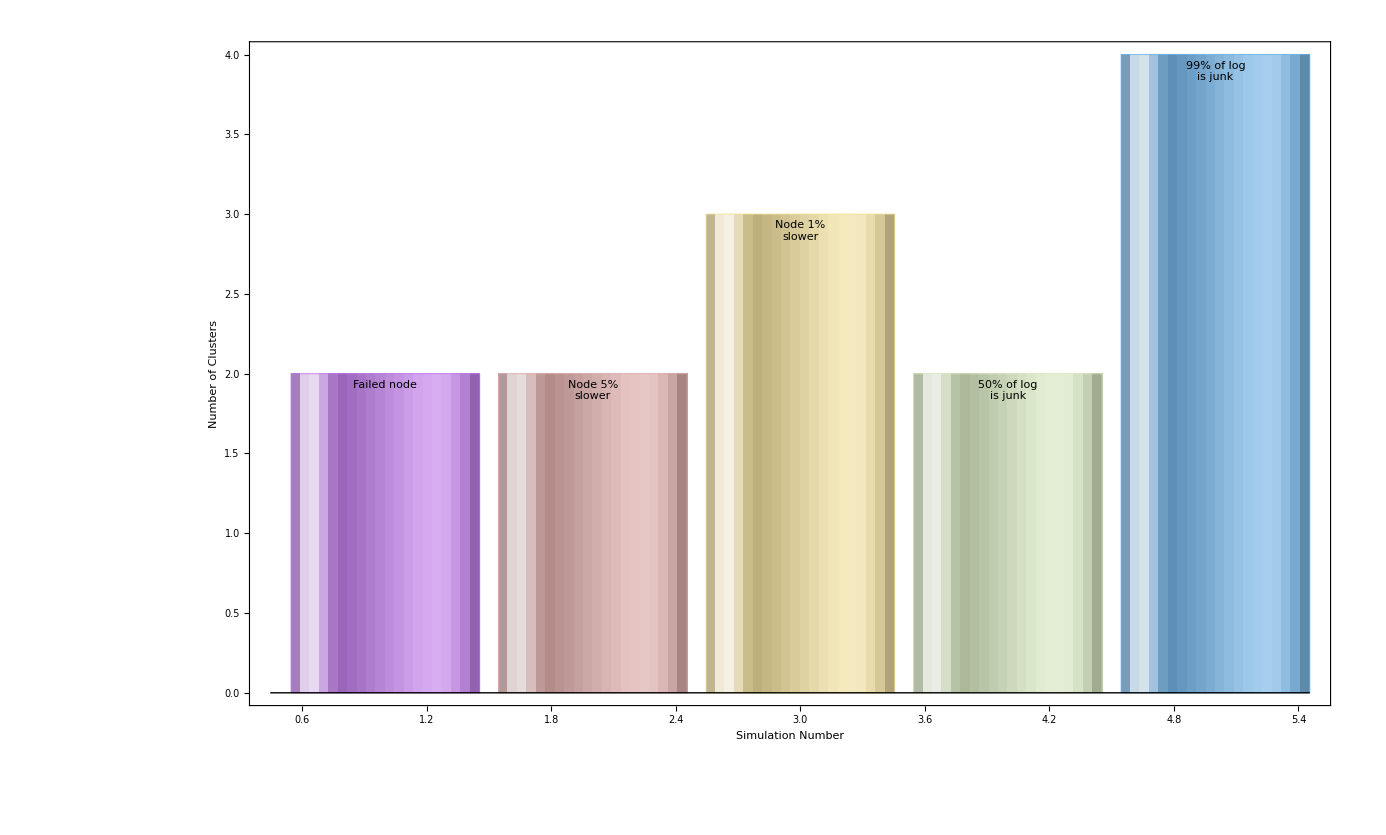

```mathematica
ex={{"Failed node",2},{"Node 5%\nslower",2},{"Node 1%\nslower", 3},{"50% of log\nis junk", 2}, {"99% of log\nis junk", 4}}
BarChart[Last[#]&/@ex,ChartLabels->Placed[(First[#]&/@ex),Top],Frame->True,ChartElementFunction->"GlassRectangle",Axes->True,ChartStyle->"Pastel",FrameLabel->{"Simulation Number" ,"Number of Clusters"},BaseStyle->{FontSize->40,FontFamily->"Calibri"}]
```